Thu 5 Dec 2024 21:12:38 ◆ M. Hosein Gholami ◆ [mohogholami@theorie.ikp.physik.tu-darmstadt.de ](mailto:mohogholami@theorie.ikp.physik.tu-darmstadt.de ) ◆ TU Darmstadt

# Two flavour NJL model

Definition of the model

```mathematica
(*Define fundamental constants and parameters*)
lambda=587.9;(*A characteristic momentum scale*)
Lambda=10*lambda;(*An extended momentum cutoff,10 times lambda*)
Gin=2.44/lambda^2;(*Coupling constant Gin,inversely proportional to lambda squared*)
bareMass=5.6;(*Bare mass parameter*)
(*Define the energy dispersion relation*)
ene=Sqrt[p^2+M^2];(*Energy as a function of momentum p and mass m*)
(*Vacuum integral calculation*)
vacInt=-2*3/(Pi^2)*p^2*ene;
(*vacInt represents the vacuum contribution to the effective potential.
-The factor-2 accounts for fermionic degrees of freedom (e.g.,spin and particle-antiparticle).
-The factor 3 arises from degeneracy factors (e.g.,color charge in QCD).
-The integral involves p^2 times the energy ene,normalized by Pi squared.*)

(*Thermal integral calculation*)
thermalInt=-2*3/(Pi^2)*p^2*(T*Log[1+Exp[-((ene+μ)/T)]]+T*Log[1+Exp[-((ene-μ)/T)]]);
(*thermalInt represents the thermal contribution to the effective potential.-Similar prefactors as vacInt for fermionic degrees of freedom.-Involves thermal distributions for particles and antiparticles with chemical potential mu.-The expressions inside the logs account for Fermi-Dirac statistics at temperature t.*)

(*Define the effective potential OmegaEff as a function of temperature T,chemical potential μ,and mass M*)
OmegaEff[T_,μ_,M_]:=Quiet@NIntegrate[-(6 p^2 (T Log[1+ⅇ^(-(√(M^2+p^2)-μ)/T)]+T Log[1+ⅇ^(-(√(M^2+p^2)+μ)/T)]))/π^2,{p,0,Lambda},WorkingPrecision->20]+NIntegrate[-(6 p^2 √(M^2+p^2))/π^2,{p,0,lambda},WorkingPrecision->20]+(M-bareMass)^2/(4*Gin);

(*OmegaEff combines both thermal and vacuum contributions to the effective potential.Components:
1. Thermal Contribution:
	-Integrates from p 0 to p Lambda (high momentum cutoff). Ideal Lambda= Infinity by the RG consistency.
  -The integrand includes thermal logarithmic terms for fermions with energy sqrt(M^2+p^2) and chemical potential mu.
  -The factor 6 arises from degeneracy factors (e.g.,spin,color).-The result is multiplied by-1/Pi^2.
    -Quiet suppresses any warnings during numerical integration.-PrecisionGoal->16 ensures high numerical precision.
2. Vacuum Contribution:
	-Integrates from p 0 to p=lambda (lower momentum cutoff).
	-The integrand is the negative of (6 p^2*energy) divided by Pi squared.-Represents the zero-temperature vacuum energy contribution.3. Mass Term Correction:-(M-bareMass)^2/(4*Gin)-Represents the correction to the mass parameter due to interactions,scaled by the coupling constant Gin.The overall OmegaEff is the sum of thermal,vacuum,and mass correction terms,representing the effective potential at temperature T,chemical potential mu,and mass M.*)
(*gap equation*)
DMOmegaEff[T_,μ_,M_]:=Quiet@NIntegrate[(6 (ⅇ^((√(M^2+p^2))/T)+2 ⅇ^(μ/T)+ⅇ^((√(M^2+p^2)+2 μ)/T)) M p^2)/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T)) (1+ⅇ^((√(M^2+p^2)+μ)/T)) √(M^2+p^2) π^2),{p,0,Lambda},WorkingPrecision->20]+NIntegrate[-(6 M p^2)/(√(M^2+p^2) π^2),{p,0,lambda},WorkingPrecision->20]+(-bareMass+M)/(2 Gin);
```

A plot of the effective potential as function of M at T=μ=10MeV

NIntegrate::precw: The precision of the argument function (-(6 p^2 √(249980.+p^2))/π^2) is less than WorkingPrecision (20.).

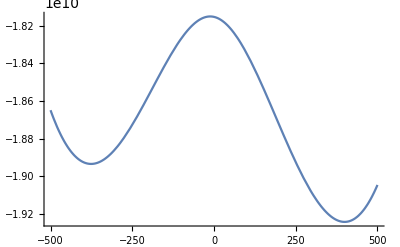

```mathematica
Plot[OmegaEff[10,10,x],{x,-500,500}]
```

Minimizer set up

```mathematica
Omega0=-1.924213155454617*^10;(*this is the vaccum vale of the potential which we shift*)
Sol[T0_?NumericQ,μ0_?NumericQ,mstart10_?NumericQ,mstart20_?NumericQ]:=Quiet@Module[{Omega0=Omega0,μ=μ0,T=T0,mstart1=mstart10,mstart2=mstart20,mins1,mins2,param1,param2},(*Find the minimum of the effective potential with respect to m,starting from mstart1*)mins1=FindRoot[{DMOmegaEff[T,μ,m]},{{m,mstart1}}];
(*Find the minimum of the effective potential with respect to m,starting from mstart2*)mins2=FindRoot[{DMOmegaEff[T,μ,m]},{{m,mstart2}}];
(*Extract the physical parameter (mass) and the shifted potential value for the first minimum*)param1={Abs[m/. mins1[[1]]],OmegaEff[T,μ,Abs[m/. mins1[[1]]]]-Omega0};
(*Extract the physical parameter (mass) and the shifted potential value for the second minimum*)param2={Abs[m/. mins2[[1]]],OmegaEff[T,μ,Abs[m/. mins2[[1]]]]-Omega0};
(*Compare the two minima based on the value of the shifted potential and return the one with the smallest value.Return only the mass and the shifted potential for the selected minimum.*)TakeSmallestBy[{param1,param2},Last,1][[1]][[1;;2]]]
```

Defenition of the numerical finite difference derivatives

```mathematica
FirstDerivative[data_List]:=Module[{n,h,derivatives},n=Length[data];
h=(Last[data][[1]]-First[data][[1]])/(n-1);
(*Compute first derivative using central differences for interior points*)derivatives=Table[{data[[i,1]],(data[[i+1,2]]-data[[i-1,2]])/(2 h)},{i,2,n-1}];
derivatives];
SecondDerivative[data_List]:=Module[{n,h,derivatives},n=Length[data];
h=(Last[data][[1]]-First[data][[1]])/(n-1);
(*Compute second derivative using central differences for interior points*)derivatives=Table[{data[[i,1]],(data[[i+1,2]]-2 data[[i,2]]+data[[i-1,2]])/(h^2)},{i,2,n-1}];
derivatives];
ThirdDerivative[data_List]:=Module[{n,h,derivatives},n=Length[data];
h=(Last[data][[1]]-First[data][[1]])/(n-1);
(*Ensure there are enough points to compute third derivative*)If[n<5,Return["Not enough data points for third derivative"]];
(*Compute third derivative using central differences for interior points*)derivatives=Table[{data[[i,1]],(data[[i+2,2]]-2 data[[i+1,2]]+2 data[[i-1,2]]-data[[i-2,2]])/(2 h^3)},{i,3,n-2}];
derivatives];
```

Now we can start doing calculations

First, we solve the gap equation for a grid of chemical potentials at T=0.1 and plot it,

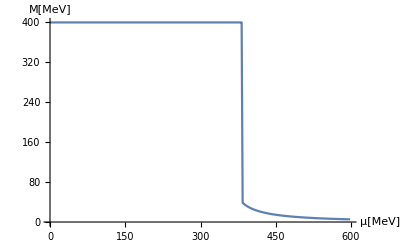

```mathematica
MassVsμlist=ParallelTable[{i,Sol[0.1,i,0,399.44277656717674][[1]]},{i,0.001,600,2}];
ListLinePlot[%,AxesLabel->{"μ[MeV]","M[MeV]"}]
```

The potential, that is \tilde c_{0,0}, we store it with 6 significant digits

```mathematica
ctilde00list=ParallelTable[{MassVsμlist[[i]][[1]],SetPrecision[Quiet@OmegaEff[0.1,MassVsμlist[[i]][[1]],MassVsμlist[[i]][[2]]]+1.924213155454617*^10,6]},{i,1,Length@MassVsμlist}];
```

First, second and third derivative of the pressure wrt μ is

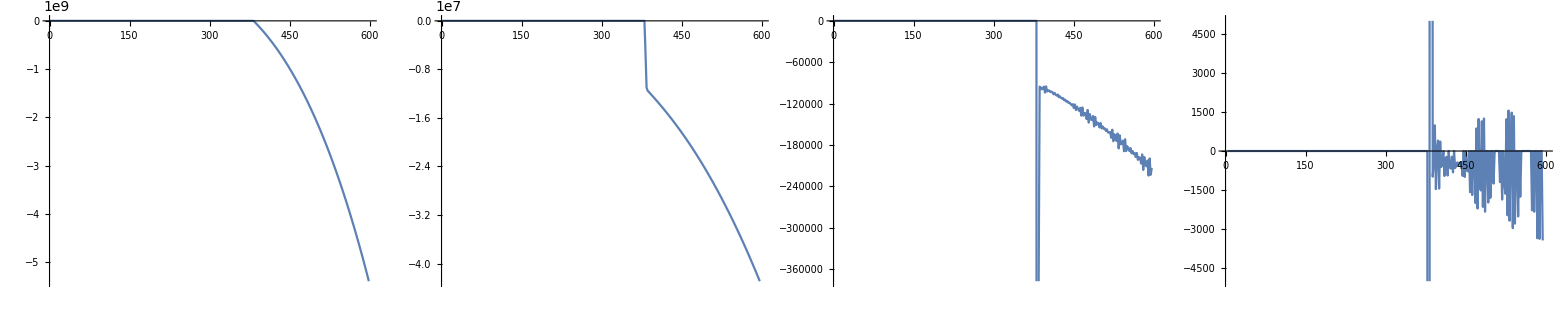

```mathematica
ListLinePlot[ctilde00list,PlotRange->{{0,600},Automatic}];
ListLinePlot[FirstDerivative[ctilde00list],PlotRange->{{0,600},Automatic}];
ListLinePlot[SecondDerivative[ctilde00list],PlotRange->{{0,600},Automatic}];
ListLinePlot[ThirdDerivative[ctilde00list],PlotRange->{{0,600},{-5000,5000}}];
Grid[{{%%%%,%%%,%%,%}}]
```

As you can see, it gets noisy for higher derivatives

# Setting up the mu derivatives

For setting up the Jacobian, we just have to introduce and define the terms we have in the Jacobian structures, here are the derivatives needed for the μ derivative of the pressure based on the calculations of the paper

```mathematica
(* first T derivative of effective potential*)
DTOmegaEff[T_,μ_,M_]:=NIntegrate[-(6 p^2 ((ⅇ^(μ/T) (√(M^2+p^2)-μ))/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T)) T)+(√(M^2+p^2)+μ)/((1+ⅇ^((√(M^2+p^2)+μ)/T)) T)+Log[1+ⅇ^((-√(M^2+p^2)+μ)/T)]+Log[1+ⅇ^(-(√(M^2+p^2)+μ)/T)]))/π^2,{p,0,Lambda},WorkingPrecision->500];
(* first μ derivative of effective potential*)
DμOmegaEff[T_,μ_,M_]:=NIntegrate[-(6 p^2 Sinh[μ/T])/(π^2 (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T])),{p,0,Lambda},WorkingPrecision->500];
(* second M,M derivative of effective potential*)
DMMOmegaEff[T_,μ_,M_]:=NIntegrate[(6 p^2 (ⅇ^((2 √(M^2+p^2))/T) p^2 T+2 ⅇ^((2 μ)/T) p^2 T+ⅇ^((2 (√(M^2+p^2)+2 μ))/T) p^2 T+ⅇ^((3 (√(M^2+p^2)+μ))/T) (-M^2 √(M^2+p^2)+p^2 T)+ⅇ^((3 √(M^2+p^2)+μ)/T) (-M^2 √(M^2+p^2)+p^2 T)+ⅇ^((√(M^2+p^2)+μ)/T) (-M^2 √(M^2+p^2)+3 p^2 T)+ⅇ^((√(M^2+p^2)+3 μ)/T) (-M^2 √(M^2+p^2)+3 p^2 T)+ⅇ^((2 (√(M^2+p^2)+μ))/T) (-4 M^2 √(M^2+p^2)+4 p^2 T)))/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T))^2 (1+ⅇ^((√(M^2+p^2)+μ)/T))^2 (M^2+p^2)^(3/2) π^2 T),{p,0,Lambda},WorkingPrecision->500]+NIntegrate[-(6 p^4)/((M^2+p^2)^(3/2) π^2),{p,0,lambda},WorkingPrecision->500]+1/(2 Gin);
(* second μ,μ derivative of effective potential*)
DμμOmegaEff[T_,μ_,M_]:=NIntegrate[-(3 p^2 (Sech[(√(M^2+p^2)-μ)/(2 T)]^2+Sech[(√(M^2+p^2)+μ)/(2 T)]^2))/(2 π^2 T),{p,0,Lambda},WorkingPrecision->500];
(* second μ,M derivative of effective potential*)
DμMOmegaEff[T_,μ_,M_]:=NIntegrate[(3 M p^2 (Sech[(√(M^2+p^2)-μ)/(2 T)]^2-Sech[(√(M^2+p^2)+μ)/(2 T)]^2))/(2 √(M^2+p^2) π^2 T),{p,0,Lambda},WorkingPrecision->500];
(* Third μ,μ,μ derivative of effective potential*)
DμμμOmegaEff[T_,μ_,M_]:=NIntegrate[(3 p^2 (3-Cosh[(2 √(M^2+p^2))/T]+2 Cosh[(√(M^2+p^2))/T] Cosh[μ/T]) Sinh[μ/T])/(π^2 T^2 (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T])^3),{p,0,Lambda},WorkingPrecision->500];
(* Third μ,μ,M derivative of effective potential*)
DμμMOmegaEff[T_,μ_,M_]:=NIntegrate[(3 M p^2 (3+2 Cosh[(√(M^2+p^2))/T] Cosh[μ/T]-Cosh[(2 μ)/T]) Sinh[(√(M^2+p^2))/T])/(√(M^2+p^2) π^2 T^2 (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T])^3),{p,0,Lambda},WorkingPrecision->500];
(* Third μ,M,M derivative of effective potential*)
DμMMOmegaEff[T_,μ_,M_]:=NIntegrate[(3 p^2 ((M^2 (3-Cosh[(2 √(M^2+p^2))/T]+2 Cosh[(√(M^2+p^2))/T] Cosh[μ/T]))/(M^2+p^2)+(2 p^2 T (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T]) Sinh[(√(M^2+p^2))/T])/((M^2+p^2)^(3/2))) Sinh[μ/T])/(π^2 T^2 (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T])^3),{p,0,Lambda},WorkingPrecision->500];
(* Third M,M,M derivative of effective potential*)
DMMMOmegaEff[T_,μ_,M_]:=NIntegrate[-1/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T))^3 (1+ⅇ^((√(M^2+p^2)+μ)/T))^3 (M^2+p^2)^(5/2) π^2 T^2)6 M p^2 (3 ⅇ^((3 √(M^2+p^2))/T) p^2 T^2+6 ⅇ^((3 μ)/T) p^2 T^2+3 ⅇ^((3 (√(M^2+p^2)+2 μ))/T) p^2 T^2+9 ⅇ^((3 √(M^2+p^2)+2 μ)/T) p^2 T (2 √(M^2+p^2)+3 T)+9 ⅇ^((3 √(M^2+p^2)+4 μ)/T) p^2 T (2 √(M^2+p^2)+3 T)-ⅇ^((5 √(M^2+p^2)+2 μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+T))-6 ⅇ^((4 √(M^2+p^2)+3 μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+T))-ⅇ^((5 √(M^2+p^2)+4 μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+T))+ⅇ^((4 √(M^2+p^2)+μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+2 T))+6 ⅇ^((2 √(M^2+p^2)+3 μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+2 T))+ⅇ^((4 √(M^2+p^2)+5 μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+2 T))-ⅇ^((2 √(M^2+p^2)+μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+4 T))-ⅇ^((2 √(M^2+p^2)+5 μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+4 T))+ⅇ^((√(M^2+p^2)+2 μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+5 T))+ⅇ^((√(M^2+p^2)+4 μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+5 T))),{p,0,Lambda},WorkingPrecision->500]+NIntegrate[(18 M p^4)/((M^2+p^2)^(5/2) π^2),{p,0,lambda},WorkingPrecision->500];
```

here, we now define the \tilde c functions of the paper for the first 3 μ derivatives of the pressure

We also define the naive derivatives , which we eventually compare to see if they are sufficient

```mathematica
ctilde01[T_,μ_,M_]:=DμOmegaEff[T,μ,M];
NAIVEctilde02[T_,μ_,M_]:=DμμOmegaEff[T,μ,M];
ctilde02[T_,μ_,M_]:=DμμOmegaEff[T,μ,M]-(DμMOmegaEff[T,μ,M])^2/DMMOmegaEff[T,μ,M];
NAIVEctilde03[T_,μ_,M_]:=DμμμOmegaEff[T,μ,M];
SECONDORDERctilde03[T_,μ_,M_]:=DμμμOmegaEff[T,μ,M]-(3(DμMOmegaEff[T,μ,M])(DμμMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M];
THIRDORDERctilde03[T_,μ_,M_]:=DμμμOmegaEff[T,μ,M]-(3(DμMOmegaEff[T,μ,M])(DμμMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M]+(3(DμMOmegaEff[T,μ,M])^2(DμMMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M]^2;

ctilde03[T_,μ_,M_]:=DμμμOmegaEff[T,μ,M]-(3(DμMOmegaEff[T,μ,M])(DμμMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M]+(3(DμMOmegaEff[T,μ,M])^2(DμMMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M]^2-((DMMMOmegaEff[T,μ,M])(DμMOmegaEff[T,μ,M])^3)/DMMOmegaEff[T,μ,M]^3;
```

plotting and comparing naive derivative of  c02 (green) with numerical finite difference (red) and our method for c02 (blue)

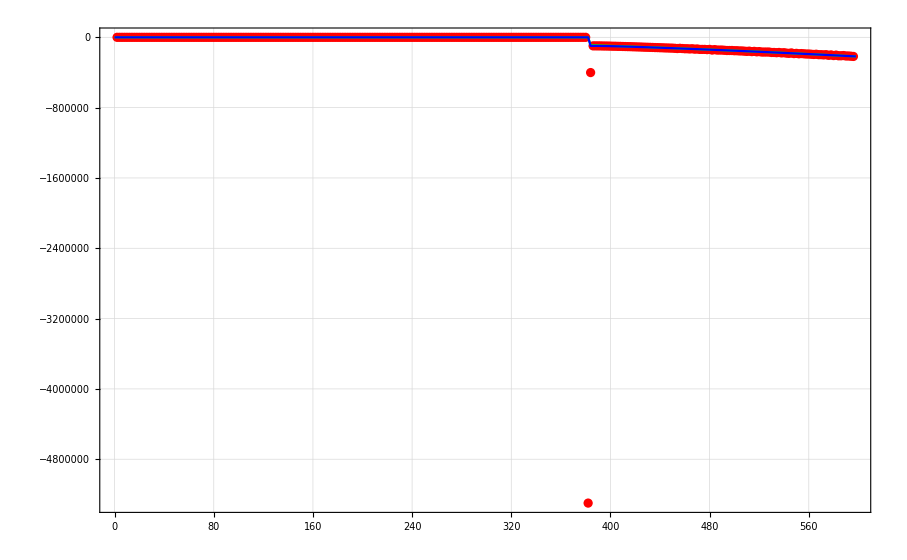

```mathematica
Naivectilde02list=Quiet@ParallelTable[{MassVsμlist[[i]][[1]],Quiet@NAIVEctilde02[0.1,MassVsμlist[[i]][[1]],MassVsμlist[[i]][[2]]]},{i,1,Length@MassVsμlist}];
ctilde02list=Quiet@ParallelTable[{MassVsμlist[[i]][[1]],Quiet@ctilde02[0.1,MassVsμlist[[i]][[1]],MassVsμlist[[i]][[2]]]},{i,1,Length@MassVsμlist}];
ListPlot[SecondDerivative[ctilde00list],PlotStyle->Red];
ListLinePlot[Naivectilde02list,PlotStyle->Green];
ListLinePlot[ctilde02list,PlotStyle->Blue];
Show[%%%,%%,%,PlotRange->{{350,600},{-70000,-220000}},Frame->True,GridLines->Automatic]
```

plotting and comparing different truncation of  c03 (green, details in the paper) with numerical finite difference (red) and our method for c03 (blue)

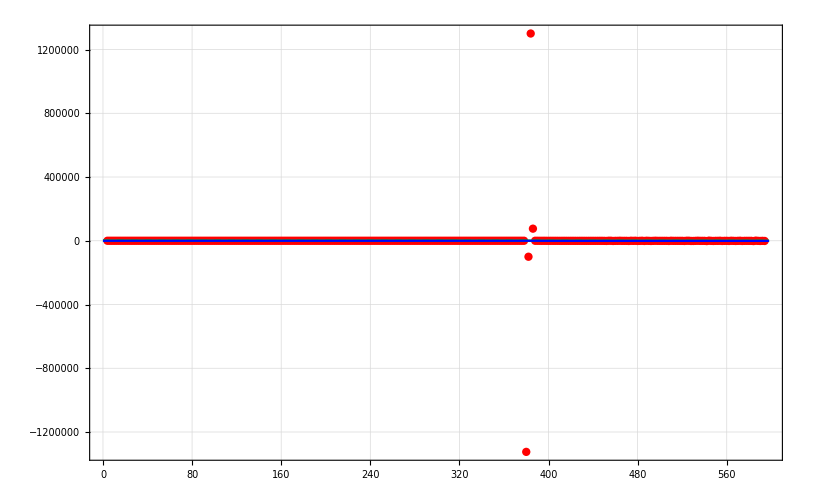

```mathematica
ListPlot[ThirdDerivative[ctilde00list],PlotStyle->Red];
ListLinePlot[Naivectilde03list,PlotStyle->Green];
ListLinePlot[SECONDORDERctilde03list,PlotStyle->Darker@Green];
ListLinePlot[THIRDORDERctilde03list,PlotStyle->{Darker@Green,Dashed}];
ListLinePlot[ctilde03list,PlotStyle->Blue];
Show[%%%%%,%%%%,%%%,%%,%,PlotRange->{{350,600},{1000,-2000}},Frame->True,GridLines->Automatic]
```

# Setting up the T derivatives

Here’s the same part as before, now for the temperature derivatives

```mathematica
DTOmegaEff[T_,μ_,M_]:=NIntegrate[-(6 p^2 ((ⅇ^(μ/T) (√(M^2+p^2)-μ))/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T)) T)+(√(M^2+p^2)+μ)/((1+ⅇ^((√(M^2+p^2)+μ)/T)) T)+Log[1+ⅇ^((-√(M^2+p^2)+μ)/T)]+Log[1+ⅇ^(-(√(M^2+p^2)+μ)/T)]))/π^2,{p,0,Lambda},WorkingPrecision->500];
DTTOmegaEff[T_,μ_,M_]:=NIntegrate[(24 ⅇ^((2 (√(M^2+p^2)+μ))/T) p^2 (-((M^2+p^2+μ^2) (1+Cosh[(√(M^2+p^2))/T] Cosh[μ/T]))+2 √(M^2+p^2) μ Sinh[(√(M^2+p^2))/T] Sinh[μ/T]))/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T))^2 (1+ⅇ^((√(M^2+p^2)+μ)/T))^2 π^2 T^3),{p,0,Lambda},WorkingPrecision->500];
DTTTOmegaEff[T_,μ_,M_]:=NIntegrate[1/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T))^3 (1+ⅇ^((√(M^2+p^2)+μ)/T))^3 π^2 T^5)24 ⅇ^((2 (√(M^2+p^2)+μ))/T) p^2 ((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T)) (1+ⅇ^((√(M^2+p^2)+μ)/T)) (M^2+p^2-μ^2) (√(M^2+p^2) Cosh[μ/T] Sinh[(√(M^2+p^2))/T]-μ Cosh[(√(M^2+p^2))/T] Sinh[μ/T])-3 (ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T)) (1+ⅇ^((√(M^2+p^2)+μ)/T)) T (-((M^2+p^2+μ^2) (1+Cosh[(√(M^2+p^2))/T] Cosh[μ/T]))+2 √(M^2+p^2) μ Sinh[(√(M^2+p^2))/T] Sinh[μ/T])+2 ⅇ^((√(M^2+p^2)+μ)/T) (ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T)) (√(M^2+p^2)+μ) (-((M^2+p^2+μ^2) (1+Cosh[(√(M^2+p^2))/T] Cosh[μ/T]))+2 √(M^2+p^2) μ Sinh[(√(M^2+p^2))/T] Sinh[μ/T])-2 (ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T)) (1+ⅇ^((√(M^2+p^2)+μ)/T)) (√(M^2+p^2)+μ) (-((M^2+p^2+μ^2) (1+Cosh[(√(M^2+p^2))/T] Cosh[μ/T]))+2 √(M^2+p^2) μ Sinh[(√(M^2+p^2))/T] Sinh[μ/T])-2 (1+ⅇ^((√(M^2+p^2)+μ)/T)) (-ⅇ^((√(M^2+p^2))/T) √(M^2+p^2)-ⅇ^(μ/T) μ) (-((M^2+p^2+μ^2) (1+Cosh[(√(M^2+p^2))/T] Cosh[μ/T]))+2 √(M^2+p^2) μ Sinh[(√(M^2+p^2))/T] Sinh[μ/T])),{p,0,Lambda},WorkingPrecision->500];
DTMOmegaEff[T_,μ_,M_]:=NIntegrate[(6 M p^2 (√(M^2+p^2)+√(M^2+p^2) Cosh[(√(M^2+p^2))/T] Cosh[μ/T]-μ Sinh[(√(M^2+p^2))/T] Sinh[μ/T]))/(√(M^2+p^2) π^2 T^2 (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T])^2),{p,0,Lambda},WorkingPrecision->500];
DTMMOmegaEff[T_,μ_,M_]:=NIntegrate[1/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T))^3 (1+ⅇ^((√(M^2+p^2)+μ)/T))^3 (M^2+p^2)^(3/2) π^2 T^3)6 ⅇ^((√(M^2+p^2)+μ)/T) p^2 (-6 ⅇ^((3 √(M^2+p^2)+2 μ)/T) (M^2+p^2) (M^2-√(M^2+p^2) T)+6 ⅇ^((√(M^2+p^2)+2 μ)/T) (M^2+p^2) (M^2+√(M^2+p^2) T)+ⅇ^(μ/T) (M^4+M^2 (p^2+√(M^2+p^2) (T-μ))+p^2 T (√(M^2+p^2)-μ))+ⅇ^((3 √(M^2+p^2)+4 μ)/T) (M^4+M^2 (p^2+√(M^2+p^2) (T-μ))+p^2 T (√(M^2+p^2)-μ))+6 ⅇ^((2 √(M^2+p^2)+3 μ)/T) √(M^2+p^2) (p^2 T+M^2 (T-μ))+6 ⅇ^((2 √(M^2+p^2)+μ)/T) √(M^2+p^2) (p^2 T+M^2 (T+μ))+ⅇ^((4 √(M^2+p^2)+μ)/T) (-M^4+p^2 T (√(M^2+p^2)+μ)-M^2 (p^2+√(M^2+p^2) (-T+μ)))+ⅇ^((√(M^2+p^2)+4 μ)/T) (-M^4+p^2 T (√(M^2+p^2)+μ)-M^2 (p^2+√(M^2+p^2) (-T+μ)))+ⅇ^((√(M^2+p^2))/T) (-M^4+p^2 T (√(M^2+p^2)-μ)+M^2 (-p^2+√(M^2+p^2) (T+μ)))+ⅇ^((4 √(M^2+p^2)+3 μ)/T) (-M^4+p^2 T (√(M^2+p^2)-μ)+M^2 (-p^2+√(M^2+p^2) (T+μ)))+ⅇ^((3 √(M^2+p^2))/T) (M^4+p^2 T (√(M^2+p^2)+μ)+M^2 (p^2+√(M^2+p^2) (T+μ)))+ⅇ^((3 μ)/T) (M^4+p^2 T (√(M^2+p^2)+μ)+M^2 (p^2+√(M^2+p^2) (T+μ)))),{p,0,Lambda},WorkingPrecision->500];
DTTMOmegaEff[T_,μ_,M_]:=NIntegrate[-1/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T))^3 (1+ⅇ^((√(M^2+p^2)+μ)/T))^3 √(M^2+p^2) π^2 T^4)6 ⅇ^((√(M^2+p^2)+μ)/T) M p^2 (12 ⅇ^((2 √(M^2+p^2)+3 μ)/T) √(M^2+p^2) (T-μ)+12 ⅇ^((2 √(M^2+p^2)+μ)/T) √(M^2+p^2) (T+μ)-6 ⅇ^((3 √(M^2+p^2)+2 μ)/T) (M^2+p^2-2 √(M^2+p^2) T+μ^2)+6 ⅇ^((√(M^2+p^2)+2 μ)/T) (M^2+p^2+2 √(M^2+p^2) T+μ^2)+ⅇ^(μ/T) (M^2+p^2+2 √(M^2+p^2) T-2 √(M^2+p^2) μ-2 T μ+μ^2)+ⅇ^((3 √(M^2+p^2)+4 μ)/T) (M^2+p^2+2 √(M^2+p^2) T-2 √(M^2+p^2) μ-2 T μ+μ^2)-ⅇ^((√(M^2+p^2))/T) (M^2+p^2-2 √(M^2+p^2) T-2 √(M^2+p^2) μ+2 T μ+μ^2)-ⅇ^((4 √(M^2+p^2)+3 μ)/T) (M^2+p^2-2 √(M^2+p^2) T-2 √(M^2+p^2) μ+2 T μ+μ^2)-ⅇ^((4 √(M^2+p^2)+μ)/T) (M^2+p^2-2 T (√(M^2+p^2)+μ)+μ (2 √(M^2+p^2)+μ))-ⅇ^((√(M^2+p^2)+4 μ)/T) (M^2+p^2-2 T (√(M^2+p^2)+μ)+μ (2 √(M^2+p^2)+μ))+ⅇ^((3 √(M^2+p^2))/T) (M^2+p^2+2 T (√(M^2+p^2)+μ)+μ (2 √(M^2+p^2)+μ))+ⅇ^((3 μ)/T) (M^2+p^2+2 T (√(M^2+p^2)+μ)+μ (2 √(M^2+p^2)+μ))),{p,0,Lambda},WorkingPrecision->500];
DμOmegaEff[T_,μ_,M_]:=NIntegrate[-(6 p^2 Sinh[μ/T])/(π^2 (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T])),{p,0,Lambda},WorkingPrecision->500];
DMMOmegaEff[T_,μ_,M_]:=NIntegrate[(6 p^2 (ⅇ^((2 √(M^2+p^2))/T) p^2 T+2 ⅇ^((2 μ)/T) p^2 T+ⅇ^((2 (√(M^2+p^2)+2 μ))/T) p^2 T+ⅇ^((3 (√(M^2+p^2)+μ))/T) (-M^2 √(M^2+p^2)+p^2 T)+ⅇ^((3 √(M^2+p^2)+μ)/T) (-M^2 √(M^2+p^2)+p^2 T)+ⅇ^((√(M^2+p^2)+μ)/T) (-M^2 √(M^2+p^2)+3 p^2 T)+ⅇ^((√(M^2+p^2)+3 μ)/T) (-M^2 √(M^2+p^2)+3 p^2 T)+ⅇ^((2 (√(M^2+p^2)+μ))/T) (-4 M^2 √(M^2+p^2)+4 p^2 T)))/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T))^2 (1+ⅇ^((√(M^2+p^2)+μ)/T))^2 (M^2+p^2)^(3/2) π^2 T),{p,0,Lambda},WorkingPrecision->500]+NIntegrate[-(6 p^4)/((M^2+p^2)^(3/2) π^2),{p,0,lambda},WorkingPrecision->500]+1/(2 Gin);
DμμOmegaEff[T_,μ_,M_]:=NIntegrate[-(3 p^2 (Sech[(√(M^2+p^2)-μ)/(2 T)]^2+Sech[(√(M^2+p^2)+μ)/(2 T)]^2))/(2 π^2 T),{p,0,Lambda},WorkingPrecision->500];
DμMOmegaEff[T_,μ_,M_]:=NIntegrate[(3 M p^2 (Sech[(√(M^2+p^2)-μ)/(2 T)]^2-Sech[(√(M^2+p^2)+μ)/(2 T)]^2))/(2 √(M^2+p^2) π^2 T),{p,0,Lambda},WorkingPrecision->500];
DμμμOmegaEff[T_,μ_,M_]:=NIntegrate[(3 p^2 (3-Cosh[(2 √(M^2+p^2))/T]+2 Cosh[(√(M^2+p^2))/T] Cosh[μ/T]) Sinh[μ/T])/(π^2 T^2 (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T])^3),{p,0,Lambda},WorkingPrecision->500];
DμμMOmegaEff[T_,μ_,M_]:=NIntegrate[(3 M p^2 (3+2 Cosh[(√(M^2+p^2))/T] Cosh[μ/T]-Cosh[(2 μ)/T]) Sinh[(√(M^2+p^2))/T])/(√(M^2+p^2) π^2 T^2 (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T])^3),{p,0,Lambda},WorkingPrecision->500];
DμMMOmegaEff[T_,μ_,M_]:=NIntegrate[(3 p^2 ((M^2 (3-Cosh[(2 √(M^2+p^2))/T]+2 Cosh[(√(M^2+p^2))/T] Cosh[μ/T]))/(M^2+p^2)+(2 p^2 T (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T]) Sinh[(√(M^2+p^2))/T])/((M^2+p^2)^(3/2))) Sinh[μ/T])/(π^2 T^2 (Cosh[(√(M^2+p^2))/T]+Cosh[μ/T])^3),{p,0,Lambda},WorkingPrecision->500];
DMMMOmegaEff[T_,μ_,M_]:=NIntegrate[-1/((ⅇ^((√(M^2+p^2))/T)+ⅇ^(μ/T))^3 (1+ⅇ^((√(M^2+p^2)+μ)/T))^3 (M^2+p^2)^(5/2) π^2 T^2)6 M p^2 (3 ⅇ^((3 √(M^2+p^2))/T) p^2 T^2+6 ⅇ^((3 μ)/T) p^2 T^2+3 ⅇ^((3 (√(M^2+p^2)+2 μ))/T) p^2 T^2+9 ⅇ^((3 √(M^2+p^2)+2 μ)/T) p^2 T (2 √(M^2+p^2)+3 T)+9 ⅇ^((3 √(M^2+p^2)+4 μ)/T) p^2 T (2 √(M^2+p^2)+3 T)-ⅇ^((5 √(M^2+p^2)+2 μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+T))-6 ⅇ^((4 √(M^2+p^2)+3 μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+T))-ⅇ^((5 √(M^2+p^2)+4 μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+T))+ⅇ^((4 √(M^2+p^2)+μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+2 T))+6 ⅇ^((2 √(M^2+p^2)+3 μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+2 T))+ⅇ^((4 √(M^2+p^2)+5 μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+2 T))-ⅇ^((2 √(M^2+p^2)+μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+4 T))-ⅇ^((2 √(M^2+p^2)+5 μ)/T) (M^4+M^2 p^2-3 p^2 T (√(M^2+p^2)+4 T))+ⅇ^((√(M^2+p^2)+2 μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+5 T))+ⅇ^((√(M^2+p^2)+4 μ)/T) (M^4+M^2 p^2+3 p^2 T (√(M^2+p^2)+5 T))),{p,0,Lambda},WorkingPrecision->500]+NIntegrate[(18 M p^4)/((M^2+p^2)^(5/2) π^2),{p,0,lambda},WorkingPrecision->500];
```

```mathematica
ctilde10[T_,μ_,M_]:=DTOmegaEff[T,μ,M];
```

```mathematica
NAIVEctilde20[T_,μ_,M_]:=DTTOmegaEff[T,μ,M];
```

```mathematica
ctilde02[T_,μ_,M_]:=DTTOmegaEff[T,μ,M]-(DTMOmegaEff[T,μ,M])^2/DMMOmegaEff[T,μ,M];
NAIVEctilde30[T_,μ_,M_]:=DTTTOmegaEff[T,μ,M];
SECONDORDERctilde30[T_,μ_,M_]:=DTTTOmegaEff[T,μ,M]-(3(DTMOmegaEff[T,μ,M])(DTTMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M];
THIRDORDERctilde30[T_,μ_,M_]:=DTTTOmegaEff[T,μ,M]-(3(DTMOmegaEff[T,μ,M])(DTTMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M]+(3(DTMOmegaEff[T,μ,M])^2(DTMMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M]^2;

ctilde30[T_,μ_,M_]:=DTTTOmegaEff[T,μ,M]-(3(DTMOmegaEff[T,μ,M])(DTTMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M]+(3(DTMOmegaEff[T,μ,M])^2(DTMMOmegaEff[T,μ,M]))/DMMOmegaEff[T,μ,M]^2-((DMMMOmegaEff[T,μ,M])(DTMOmegaEff[T,μ,M])^3)/DMMOmegaEff[T,μ,M]^3;
```

```mathematica
ctilde01list=ParallelTable[{MassVsTlistmu0[[i]][[1]],Quiet@ctilde01[0.1,MassVsμlist[[i]][[1]],MassVsμlist[[i]][[2]]]},{i,1,Length@MassVsμlist}];
ListLinePlot@%
ParallelTable[{MassVsμlist[[i]][[1]],Quiet@DμμOmegaEff[0.1,MassVsμlist[[i]][[1]],MassVsμlist[[i]][[2]]]},{i,1,Length@MassVsμlist}];
ListLinePlot@%
ParallelTable[{MassVsμlist[[i]][[1]],Quiet@DμMOmegaEff[0.1,MassVsμlist[[i]][[1]],MassVsμlist[[i]][[2]]]},{i,1,Length@MassVsμlist}];
ListLinePlot@%
```